# Deriving the empirical correlation function and fitting a curve to it

## Translating from “Towards a unified descriptive theory for spatial ecology”

M Scott & M Osmond
2016 January 21

## Made-up data

Define the spatial extent of the area of interest (e.g., Barro Colorado Island)

```mathematica
{Lx,Ly}={1000,500}; (*total x and y distance of area of interest, ie a grid with length Lx and width Ly*)
Asub=100;(*space between coordinates, ie we chop up the total area into squares with length Asub; best if this divides the total space nicely, ie Lx/Asub and Ly/Asub are integers*)
```

Make up the data (because the authors suck at making it available)

```mathematica
numplots=10000;(*number of plots/datapoints*)
data=Table[{{RandomVariate[UniformDistribution[{0,Lx}]],RandomVariate[UniformDistribution[{0,Ly}]]},RandomInteger[{1,3}],RandomInteger[10]},{i,1,numplots}];
(*(x,y) locations of each plot, species code of each plot,abundance of that species in each plot*)
```

Get each variable of interest from data table

```mathematica
gx=Table[Transpose[data][[1]][[i,1]],{i,1,numplots}]; (*x coordinates of all plots*)
gy=Table[Transpose[data][[1]][[i,2]],{i,1,numplots}]; (*y coordinates of all plots*)
sp=Transpose[data][[2]];(*species code for each plot*)
ab=Transpose[data][[3]];(*species abundance at each plot*)
```

Some summary statistics of the data

```mathematica
Uspecie=Union[sp];(*vector of species IDs*)
Nspecies=Length[Uspecie];(*total number of species*)
TotAbundance=Total[ab];(*total abundance, across all species*)
```

Defining the coordinate system of the area

```mathematica
allpos=Tuples[{Range[Lx/Asub],Range[Ly/Asub]}]; (*coordinates, in translated form, ie. {1,1}, {1,2}, ..., {2,1}, {2,2}, ..., {m,n}*)
xyCpos=Flatten[Table[{(2 i+1)/2,(2 j+1)/2}// N,{i,0,(Lx/Asub)-1,1},{j,0,(Ly/Asub)-1,1}],1];(*halfway points between coordinates, which we use later to derive the distances between centers of each "bin" (area below (south) and to left (west) of each coordinate*)
allpair=Tuples[{allpos,allpos}];(*pairs of each translated coordinate with each other, e.g., {{1,1},{1,1}}*)
nplot=Range[Length[allpos]]; (*total number of coordinates/bins*)
```

Locations of plots (the bin they are in)

```mathematica
Xpos[p_]:=Flatten[Position[gx,x_?(Asub*(p-1) ≤ #<Asub*p&)],1](*which plots (their position in the data vector) have x location between two coordinates, for all pairs of x coordinates; for p between 1 and Lx/Asub*)
Ypos[q_]:=Flatten[Position[gy,x_?(Asub*(q-1) ≤ #<Asub*q&)],1](*which plots have y location between two coordinates, for all pairs of y coordinates; for q between 1 and Ly/Asub*)
rule1=Flatten[Table[{allpos[[i]] -> nplot[[i]]},{i,1,Length[allpos]}],1];(*translate from coordinates (tuple) to single identifying number*)
rule2=Flatten[Table[{nplot[[i]] -> allpos[[i]]},{i,1,Length[allpos]}],1];(*translate back*)
XYpos[{p_,q_}]:=Intersection[Xpos[p],Ypos[q]];(*which plots have location (x,y) within (x(p-1),x p) and (y(p-1), y p)*)
possub=ParallelMap[XYpos,allpos];(*which plots fall in which bin (e.g., (x,y)=(321,434), with Asub=100, would fall in (400,500)*)
```

Which species are where

```mathematica
XYS[i_]:=Transpose[{gx[[possub[[i]]]],gy[[possub[[i]]]],sp[[possub[[i]]]]}];(*gives (x,y) location of plots, and sp code, in each bin*)
SabA[i_]:=Count[sp[[possub[[i]]]],#]&/@ Uspecie (*number of plots with each species in each bin*)
SA[i_]:=Boole/@ (MemberQ[sp[[possub[[i]]]],#]&/@ Uspecie) (*1 if at least one plot with a species in given bin, ie presence/absence in bin*)
Spos=Table[SA[i],{i,1,Length[possub]}];(*table with all bins*)
```

Covariance in species abundance by distances

```mathematica
dist[{i_,j_}]:=Sqrt[Total[(Abs[xyCpos[[i]]-xyCpos[[j]]])^2]] (*Euclidean distance between center of two bins (in translated space; need to multiply by Asub to get real distances, which we do later)*)
index[{i_,j_}]:={i,j}(*not sure what this does, but doesnt hurt*)
alldist=Map[dist,allpair/.rule1]; (*distance between center of all pairs of bins*)
rvec=Union[alldist];(*all unique distances in increasing order*)
indexpair=Map[index,allpair/. rule1];(*translate from tuples of coordinates to pairs of coordinate indices*)
posdist=Position[alldist,#]&/@ rvec;(*identify coordinate index pairs whose bin centers are given distance apart*)
Cov[{i_,j_}]:=Mean[SabA[i] SabA[j]]/(Mean[SabA[i]] Mean[SabA[j]])//N;(*"covariance" in number of plots with species across bins, note that the "covariance" is taken over all species, ie "covariance" in community composition*)
allcov=ParallelTable[Map[Cov,indexpair[[Flatten[posdist[[i]],1]]]],{i,1,Length[rvec]}];(*covaraiance in number of plots with species at each distance*)
```

Our empirical correlation function

```mathematica
empPCF=Transpose[{rvec*Asub,Map[Mean,allcov]}];(*empirical correlation function, PCF; first element of each pair is the (untranslated) distance between the center of two bins (rvec*Asub), the second element is the mean covariance in number of plots with species across all pairs of bins that distance apart*)
```

which looks like this

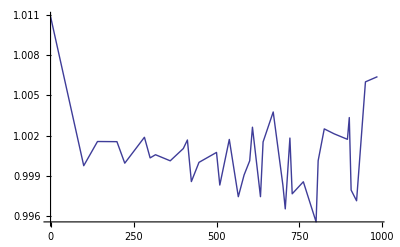

```mathematica
ListPlot[empPCF,Joined->True]
```

Fitting the function to the data

```mathematica
g[r_]:=1+1/(2π)(ρ/λ)^2 BesselK[0,r/λ](*function to fit to the empirical PCF*)
λ=.;(*what does this do?*)
ρ=.;
fitcor=NonlinearModelFit[Rest[empPCF],g[r],{{λ,10^9},{ρ,0.1}},r];(*fit the function, with some parameter guesses*)
```

NonlinearModelFit::nrlnum: The function value {0.000244287  - 9.23144×10^-20\ ⅈ, -0.00155574 - 9.23144×10^-20\ ⅈ, -0.00154485 - 9.23144×10^-20\ ⅈ, 0.0000557618  - 9.23144×10^-20\ ⅈ, -0.00187199 - 9.23144×10^-20\ ⅈ, « 27 », -0.00333753 - 9.23144×10^-20\ ⅈ, 0.00205662  - 9.23144×10^-20\ ⅈ, 0.00285256  - 9.23144×10^-20\ ⅈ, -0.00599376 - 9.23144×10^-20\ ⅈ, -0.00638056 - 9.23144×10^-20\ ⅈ} is not a list of real numbers with dimensions {37} at {λ, ρ} = {-5.90241×10^8, 0.253618}.

How good is the fit?

```mathematica
Grid[Transpose[{#,fitcor[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment -> Left](*stats for fit*)
```

AdjustedRSquared | 0.999994
AIC | -334.676
BIC | -329.844
RSquared | 0.999994

What are our parameter estimates?

```mathematica
fitcor["ParameterTable"](*stats for parameter estimates*)
σλ1=fitcor["ParameterTableEntries"][[1,2]];(*standard error for lambda*)
σρ1=fitcor["ParameterTableEntries"][[2,2]];(*standard error for rho*)(*standard error for rho*)
```

| Estimate | Standard Error | t-Statistic | P-Value
λ | -5.90241×10^8 | 2.18574×10^26+0. ⅈ | -2.70042×10^-18+0. ⅈ | 1
ρ | 0.253618 | 9.07385×10^16-7.11121×10^14 ⅈ | 2.79487×10^-18+2.19035×10^-20 ⅈ | 1.-1.96009×10^-19 ⅈ

Or if you like confidence intervals better...

```mathematica
fitcor["ParameterConfidenceIntervalTable"](*get confidence intervals too*)
```

| Estimate | Standard Error | Confidence Interval
λ | -5.90241×10^8 | 2.18574×10^26+0. ⅈ | {-4.43729×10^26+0. ⅈ,4.43729×10^26+0. ⅈ}
ρ | 0.253618 | 9.07385×10^16-7.11121×10^14 ⅈ | {-1.84209×10^17+1.44365×10^15 ⅈ,1.84209×10^17-1.44365×10^15 ⅈ}

Plot fitted curve with data points

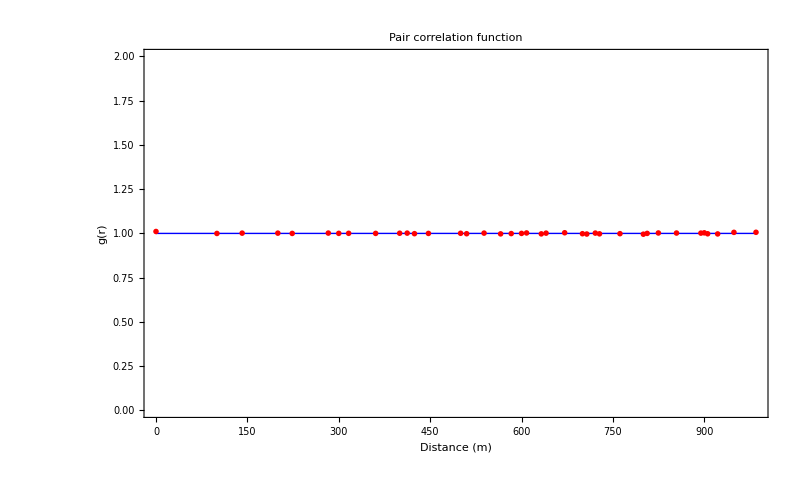

```mathematica
Plot[
fitcor[r],
{r,Min[rvec*Asub],Max[rvec*Asub]},
PlotStyle->{ Blue,Thick},
PlotRange->{{0,Max[rvec*Asub]},Automatic},
Frame ->{{True,False},{True,False}},
FrameLabel -> {"Distance (m)","g(r)"},
PlotLabel -> "Pair correlation function",
LabelStyle -> {FontFamily -> "Times",FontSize -> 12},
Prolog -> {Red,PointSize[0.005],Point/@ empPCF},
Axes->False,
ImageSize->800
]
```

Plot fitted curve with confidence bands

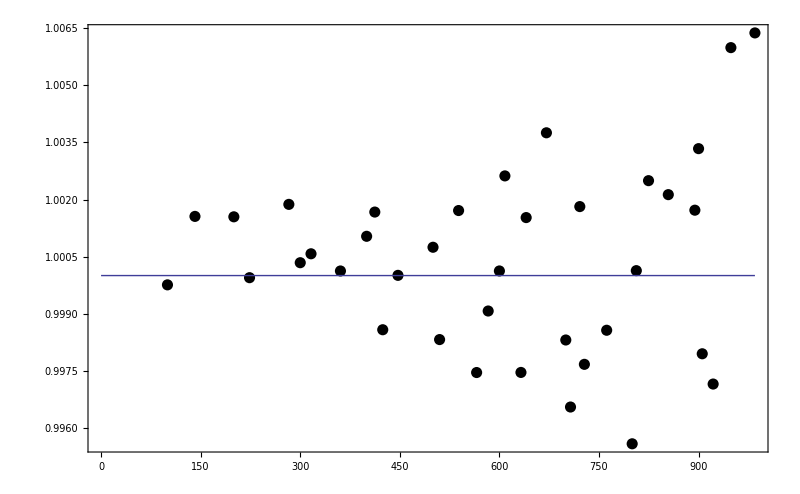

```mathematica
{bands90[x_],bands95[x_],bands99[x_],bands999[x_]} =Table[fitcor["MeanPredictionBands",ConfidenceLevel -> cl],{cl,{.9,.95,.99,.999}}];(*confidence bands*)
Show[
ListPlot[Rest[empPCF],PlotStyle->{Black,PointSize[0.01]},Axes->False],Plot[{fitcor[r],bands90[r],bands95[r],bands99[r],bands999[r]},{r,Min[rvec*Asub],Max[rvec*Asub]},Filling-> {2 ->{1},3 ->{2},4 ->{3},5 ->{4}}],
PlotRange->{{0,Max[rvec*Asub]},Automatic},
Frame->{True,True,False,False},
ImageSize->800]
```

Information for SAD and SAR plots

```mathematica
ind=Table[Total[SabA[i]],{i,1,Max[nplot]}];(*number of individuals in each plot*)
λ=.;
ρ=.;
ν=.;
α=.;
β=.;
α2p[L_]:=π (L/ρ)^2(1-(2λ)/L(BesselK[1,L/λ]BesselI[1,L/λ])/(BesselK[1,L/λ]BesselI[0,L/λ] + BesselK[0,L/λ]BesselI[1,L/λ]))^-1;
β2[L_]:=(Total[ind]/(Nspecies*Lx*Ly))*ρ^2(1-(2λ)/L(BesselK[1,L/λ]BesselI[1,L/λ])/(BesselK[1,L/λ]BesselI[0,L/λ] + BesselK[0,L/λ]BesselI[1,L/λ]));
rsapres2medp[n_,L_]:=CDF[GammaDistribution[α2p[L],β2[L]],2^(n+1)]-CDF[GammaDistribution[α2p[L],β2[L]],2^n];
sarmedp[L_]:=1-CDF[GammaDistribution[α2p[L],β2[L]],1];
SAR[r_]:=Nspecies*sarmedp[r]/sarmedp[ ((Lx*Ly)/π)^(1/2)]/.fitcor["BestFitParameters"];
SAD[n_,r_]:=Nspecies*rsapres2medp[n,r]/sarmedp[ ((Lx*Ly)/π)^(1/2)]/.fitcor["BestFitParameters"];
upRichness=NsppSamp*(sarmedp [((Lx*Ly)/π)^(1/2),dens,λ,ρ])/(sarmedp [((samp*Asp)/π)^(1/2),dens,λ,ρ]);
UPdens=Nspecies*dens/upRichness;
downSAR[r_]:=upRichness*sarmedp[r,UPdens,λ,ρ]/sarmedp[((Lx*Ly)/π)^(1/2),UPdens,λ,ρ];
```

```mathematica
(*Plot[SAR[r],{r,0,Max[rvec]},PlotRange->{0,All}]*)(*doesnt always work because fit so bad*)
```

## Simulated data

Load data from Patrick’s simulation

```mathematica
datadir="/Users/mmosmond/Documents/PHD/PCFinR/";
simdata=Import[datadir<>"SimulatedAbundances"<>".csv"];
```

The data comes with 5 columns

```mathematica
simdata[[1]]
```

{x,y,Species,Abundance,Stress_abund}

x is the x location (1:20) y is the y location (1:20), species is species ID (1:80), abundance is number of individuals of that species in plot, and stress abundance is abundance under some stressor (we will eventually want to compare model results with and without stressor).

We first drop the column names

```mathematica
simdata=Drop[simdata,{1}];
```

We then drop all rows with zero abundances

```mathematica
simdata=Select[simdata,#[[4]]≠0&];
stsimdata=Select[simdata,#[[5]]≠0&];
```

Define the spatial extent of the area of interest

```mathematica
{Lx,Ly}={20,20}; (*total x and y distance of area of interest, ie a grid with length Lx and width Ly*)
Asub=5;(*space between coordinates, ie we chop up the total area into squares with length Asub; best if this divides the total space nicely, ie Lx/Asub and Ly/Asub are integers*)
```

Get each variable of interest from data table

```mathematica
gx=Transpose[simdata][[1]];
gy=Transpose[simdata][[2]];
sp=Transpose[simdata][[3]];
ab=Transpose[simdata][[4]];

stgx=Transpose[stsimdata][[1]];
stgy=Transpose[stsimdata][[2]];
stsp=Transpose[stsimdata][[3]];
stab=Transpose[stsimdata][[5]];
```

Some summary statistics of the data

```mathematica
Uspecie=Union[sp];(*vector of species IDs*)
Nspecies=Length[Uspecie];(*total number of species*)
TotAbundance=Total[ab];(*total abundance, across all species*)

stUspecie=Union[stsp];(*vector of species IDs*)
stNspecies=Length[stUspecie];(*total number of species*)
stTotAbundance=Total[stab];
```

Defining the coordinate system of the area

```mathematica
allpos=Tuples[{Range[Lx/Asub],Range[Ly/Asub]}]; (*coordinates, in translated form, ie. {1,1}, {1,2}, ..., {2,1}, {2,2}, ..., {m,n}*)
xyCpos=Flatten[Table[{(2 i+1)/2,(2 j+1)/2}// N,{i,0,(Lx/Asub)-1,1},{j,0,(Ly/Asub)-1,1}],1];(*halfway points between coordinates, which we use later to derive the distances between centers of each "bin" (area below (south) and to left (west) of each coordinate*)
allpair=Tuples[{allpos,allpos}];(*pairs of each translated coordinate with each other, e.g., {{1,1},{1,1}}*)
nplot=Range[Length[allpos]]; (*total number of coordinates/bins*)
```

Locations of plots (the bin they are in)

```mathematica
(*Xpos[p_]:=Flatten[Position[gx,x_?(Asub*(p-1) ≤ #<Asub*p&)],1]*)
Xpos[p_]:=Flatten[Position[gx,x_?(Asub*(p-1) <#≤ Asub*p&)],1]
(*which plots (their position in the data vector) have x location between two coordinates, for all pairs of x coordinates; for p between 1 and Lx/Asub*)
stXpos[p_]:=Flatten[Position[stgx,x_?(Asub*(p-1) <#≤ Asub*p&)],1]
(*Ypos[q_]:=Flatten[Position[gy,x_?(Asub*(q-1) ≤ #<Asub*q&)],1]*)
Ypos[q_]:=Flatten[Position[gy,x_?(Asub*(q-1)<#≤Asub*q&)],1]
(*which plots have y location between two coordinates, for all pairs of y coordinates; for q between 1 and Ly/Asub*)
stYpos[q_]:=Flatten[Position[stgy,x_?(Asub*(q-1)<#≤Asub*q&)],1]
rule1=Flatten[Table[{allpos[[i]] -> nplot[[i]]},{i,1,Length[allpos]}],1];(*translate from coordinates (tuple) to single identifying number*)
rule2=Flatten[Table[{nplot[[i]] -> allpos[[i]]},{i,1,Length[allpos]}],1];(*translate back*)
XYpos[{p_,q_}]:=Intersection[Xpos[p],Ypos[q]];(*which plots have location (x,y) within (x(p-1),x p) and (y(p-1), y p)*)
stXYpos[{p_,q_}]:=Intersection[stXpos[p],stYpos[q]];
possub=ParallelMap[XYpos,allpos];(*which plots fall in which bin (e.g., (x,y)=(321,434), with Asub=100, would fall in (400,500)*)
stpossub=ParallelMap[stXYpos,allpos];
```

Which species are where

```mathematica
XYS[i_]:=Transpose[{gx[[possub[[i]]]],gy[[possub[[i]]]],sp[[possub[[i]]]]}];(*gives (x,y) location of plots, and sp code, in each bin*)
(*SabA[i_]:=Count[sp[[possub[[i]]]],#]&/@ Uspecie*) (*number of plots with each species in each bin*)
(*SabA[i_]:=(Count[sp[[possub[[i]]]],#]&/@ Uspecie)*ab[[possub[[i]]]]*)(*number of plots of each species in each bin*)
stXYS[i_]:=Transpose[{stgx[[stpossub[[i]]]],stgy[[stpossub[[i]]]],stsp[[stpossub[[i]]]]}];
SabA[i_]:=Table[Sum[ab[[possub[[i]]]][[k]],{k,Flatten[(Position[sp[[possub[[i]]]],#]&/@ Uspecie)[[j]]]}],{j,1,Dimensions[Uspecie][[1]]}] (*number of plots * abundance in that plot of each species in each bin*)
stSabA[i_]:=Table[Sum[stab[[stpossub[[i]]]][[k]],{k,Flatten[(Position[stsp[[stpossub[[i]]]],#]&/@stUspecie)[[j]]]}],{j,1,Dimensions[stUspecie][[1]]}] 
(*SA[i_]:=Boole/@ (MemberQ[sp[[possub[[i]]]],#]&/@ Uspecie) *)(*1 if at least one plot with a species in given bin, ie presence/absence in bin*)
SA[i_]:=Boole[#>0]&/@SabA[i]
stSA[i_]:=Boole[#>0]&/@stSabA[i]
Spos=Table[SA[i],{i,1,Length[possub]}];
stSpos=Table[stSA[i],{i,1,Length[stpossub]}];(*table with all bins*)
```

Covariance in species abundance by distances

```mathematica
dist[{i_,j_}]:=Sqrt[Total[(Abs[xyCpos[[i]]-xyCpos[[j]]])^2]] (*Euclidean distance between center of two bins (in translated space; need to multiply by Asub to get real distances, which we do later)*)
index[{i_,j_}]:={i,j}(*not sure what this does, but doesnt hurt*)
alldist=Map[dist,allpair/.rule1]; (*distance between center of all pairs of bins*)
rvec=Union[alldist];(*all unique distances in increasing order*)
indexpair=Map[index,allpair/. rule1];(*translate from tuples of coordinates to pairs of coordinate indices*)
posdist=Position[alldist,#]&/@ rvec;(*identify coordinate index pairs whose bin centers are given distance apart*)
Cov[{i_,j_}]:=Mean[SabA[i] SabA[j]]/(Mean[SabA[i]] Mean[SabA[j]])//N;(*"covariance" in number of plots with species across bins, note that the "covariance" is taken over all species, ie "covariance" in community composition*)
stCov[{i_,j_}]:=Mean[stSabA[i] stSabA[j]]/(Mean[stSabA[i]] Mean[stSabA[j]])//N;
```

This function can take a while to run (if too long increase Asub)

```mathematica
allcov=Table[ParallelMap[Cov,indexpair[[Flatten[posdist[[i]],1]]]],{i,1,Length[rvec]}];(*covariance in number of plots with species at each distance*)
stallcov=Table[ParallelMap[stCov,indexpair[[Flatten[posdist[[i]],1]]]],{i,1,Length[rvec]}];
```

Our empirical correlation function

```mathematica
empPCF=Transpose[{rvec*Asub,Map[Mean,allcov]}];(*empirical correlation function, PCF; first element of each pair is the (untranslated) distance between the center of two bins (rvec*Asub), the second element is the mean covariance in number of plots with species across all pairs of bins that distance apart*)
stempPCF=Transpose[{rvec*Asub,Map[Mean,stallcov]}];
```

which looks like this

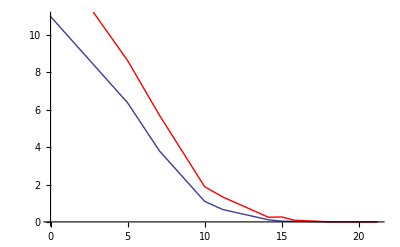

```mathematica
Show[
ListPlot[empPCF,Joined->True],
ListPlot[stempPCF,Joined->True,PlotStyle->Red]
]
```

Fitting the function to the data

```mathematica
g[r_]:=1+1/(2π)(ρ/λ)^2 BesselK[0,r/λ](*function to fit to the empirical PCF*)
λ=.;(*what does this do?*)
ρ=.;
fitcor=NonlinearModelFit[Rest[empPCF],g[r],{{λ,2},{ρ,50}},r];(*fit the function, with some parameter guesses*)
stfitcor=NonlinearModelFit[Rest[stempPCF],g[r],{{λ,2},{ρ,50}},r];
```

How good is the fit?

```mathematica
Grid[Transpose[{#,fitcor[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment -> Left](*stats for fit*)
```

AdjustedRSquared | 0.859107
AIC | 28.2027
BIC | 28.7943
RSquared | 0.890417

```mathematica
Grid[Transpose[{#,stfitcor[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment -> Left]
```

AdjustedRSquared | 0.920396
AIC | 29.2317
BIC | 29.8233
RSquared | 0.938086

What are our parameter estimates?

```mathematica
fitcor["ParameterTable"](*stats for parameter estimates*)
σλ1=fitcor["ParameterTableEntries"][[1,2]];(*standard error for lambda*)
σρ1=fitcor["ParameterTableEntries"][[2,2]];(*standard error for rho*)(*standard error for rho*)
```

| Estimate | Standard Error | t-Statistic | P-Value
λ | 2.32196 | 1.05669 | 2.19739 | 0.063977
ρ | 44.7412 | 8.22395 | 5.44035 | 0.000965882

```mathematica
stfitcor["ParameterTable"](*stats for parameter estimates*)
stσλ1=stfitcor["ParameterTableEntries"][[1,2]];(*standard error for lambda*)
stσρ1=stfitcor["ParameterTableEntries"][[2,2]];(*standard error for rho*)
```

| Estimate | Standard Error | t-Statistic | P-Value
λ | 3.00002 | 0.909216 | 3.29956 | 0.0131286
ρ | 51.2989 | 3.55881 | 14.4146 | 1.84234×10^-6

Or if you like confidence intervals better...

```mathematica
fitcor["ParameterConfidenceIntervalTable"](*get confidence intervals too*)
```

| Estimate | Standard Error | Confidence Interval
λ | 2.32196 | 1.05669 | {-0.176715,4.82063}
ρ | 44.7412 | 8.22395 | {25.2946,64.1877}

```mathematica
stfitcor["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
λ | 3.00002 | 0.909216 | {0.850062,5.14997}
ρ | 51.2989 | 3.55881 | {42.8836,59.7141}

Plot fitted curve with data points

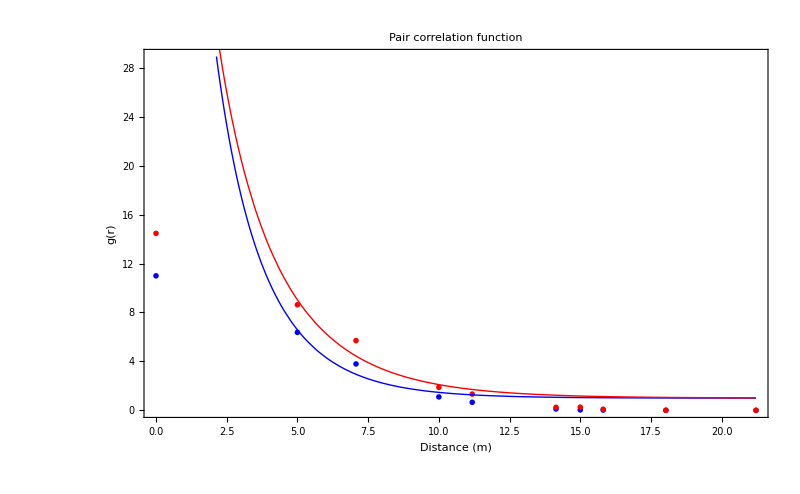

```mathematica
Show[
Plot[
fitcor[r],
{r,Min[rvec*Asub],Max[rvec*Asub]},
PlotStyle->{ Blue,Thick},
PlotRange->{{0,Max[rvec*Asub]},Automatic},
Frame ->{{True,False},{True,False}},
FrameLabel -> {"Distance (m)","g(r)"},
PlotLabel -> "Pair correlation function",
LabelStyle -> {FontFamily -> "Times",FontSize -> 12},
Prolog -> {Blue,PointSize[0.005],Point/@ empPCF},
Axes->False,
ImageSize->800
],
Plot[
stfitcor[r],
{r,Min[rvec*Asub],Max[rvec*Asub]},
PlotStyle->{ Red,Thick},
PlotRange->{{0,Max[rvec*Asub]},Automatic},
Frame ->{{True,False},{True,False}},
FrameLabel -> {"Distance (m)","g(r)"},
PlotLabel -> "Pair correlation function",
LabelStyle -> {FontFamily -> "Times",FontSize -> 12},
Prolog -> {Red,PointSize[0.005],Point/@ stempPCF},
Axes->False,
ImageSize->800
],
Prolog ->{ {Blue,PointSize[0.005],Point/@ empPCF},{Red,PointSize[0.005],Point/@ stempPCF}}
]
```

Plot fitted curve with confidence bands

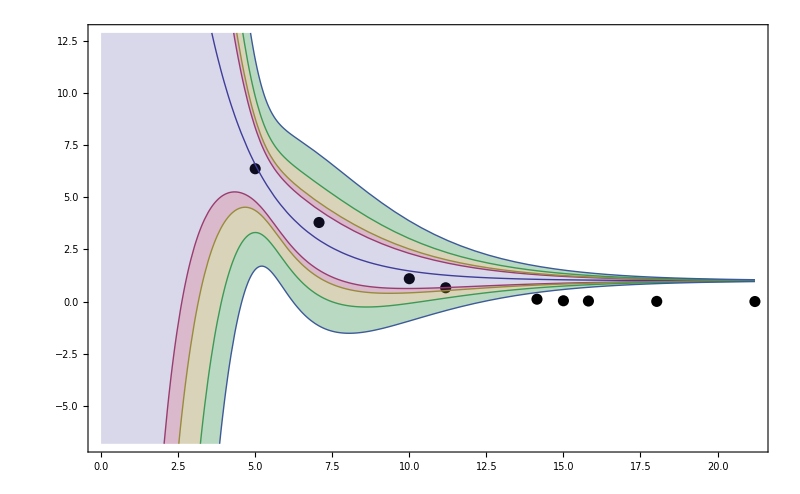

```mathematica
{bands90[x_],bands95[x_],bands99[x_],bands999[x_]} =Table[fitcor["MeanPredictionBands",ConfidenceLevel -> cl],{cl,{.9,.95,.99,.999}}];(*confidence bands*)
Show[
ListPlot[Rest[empPCF],PlotStyle->{Black,PointSize[0.01]},Axes->False],Plot[{fitcor[r],bands90[r],bands95[r],bands99[r],bands999[r]},{r,Min[rvec*Asub],Max[rvec*Asub]},Filling-> {2 ->{1},3 ->{2},4 ->{3},5 ->{4}}],
PlotRange->{{0,Max[rvec*Asub]},{0,Automatic}},
Frame->{True,True,False,False},
ImageSize->800]
```

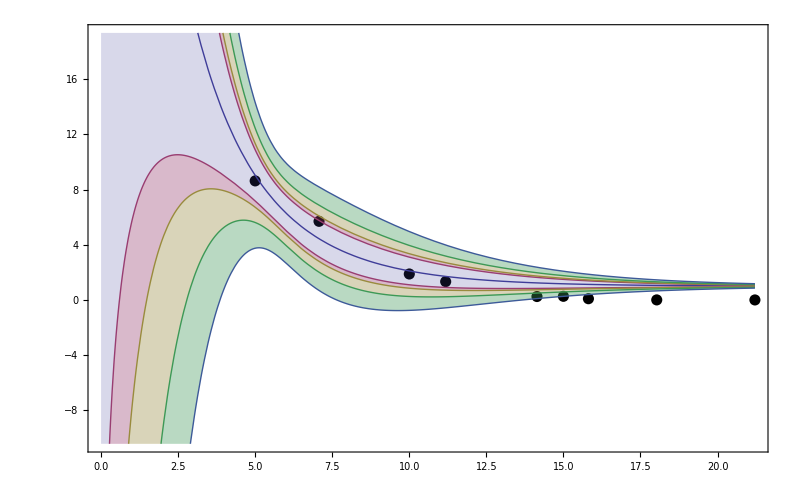

```mathematica
{stbands90[x_],stbands95[x_],stbands99[x_],stbands999[x_]} =Table[stfitcor["MeanPredictionBands",ConfidenceLevel -> cl],{cl,{.9,.95,.99,.999}}];(*confidence bands*)
Show[
ListPlot[Rest[stempPCF],PlotStyle->{Black,PointSize[0.01]},Axes->False],Plot[{stfitcor[r],stbands90[r],stbands95[r],stbands99[r],stbands999[r]},{r,Min[rvec*Asub],Max[rvec*Asub]},Filling-> {2 ->{1},3 ->{2},4 ->{3},5 ->{4}}],
PlotRange->{{0,Max[rvec*Asub]},{0,Automatic}},
Frame->{True,True,False,False},
ImageSize->800]
```

Information for SAD and SAR plots

```mathematica
ind=Table[Total[SabA[i]],{i,1,Max[nplot]}];(*number of individuals in each plot*)
λ=.;
ρ=.;
ν=.;
α=.;
β=.;
α2p[L_]:=π (L/ρ)^2(1-(2λ)/L(BesselK[1,L/λ]BesselI[1,L/λ])/(BesselK[1,L/λ]BesselI[0,L/λ] + BesselK[0,L/λ]BesselI[1,L/λ]))^-1;
β2[L_]:=(Total[ind]/(Nspecies*Lx*Ly))*ρ^2(1-(2λ)/L(BesselK[1,L/λ]BesselI[1,L/λ])/(BesselK[1,L/λ]BesselI[0,L/λ] + BesselK[0,L/λ]BesselI[1,L/λ]));
rsapres2medp[n_,L_]:=CDF[GammaDistribution[α2p[L],β2[L]],2^(n+1)]-CDF[GammaDistribution[α2p[L],β2[L]],2^n];
sarmedp[L_]:=1-CDF[GammaDistribution[α2p[L],β2[L]],1];
SAR[r_]:=Nspecies*sarmedp[r]/sarmedp[ ((Lx*Ly)/π)^(1/2)]/.fitcor["BestFitParameters"];
SAD[n_,r_]:=Nspecies*rsapres2medp[n,r]/sarmedp[ ((Lx*Ly)/π)^(1/2)]/.fitcor["BestFitParameters"];
upRichness=NsppSamp*(sarmedp [((Lx*Ly)/π)^(1/2),dens,λ,ρ])/(sarmedp [((samp*Asp)/π)^(1/2),dens,λ,ρ]);
UPdens=Nspecies*dens/upRichness;
downSAR[r_]:=upRichness*sarmedp[r,UPdens,λ,ρ]/sarmedp[((Lx*Ly)/π)^(1/2),UPdens,λ,ρ];
```

```mathematica
stind=Table[Total[stSabA[i]],{i,1,Max[nplot]}];(*number of individuals in each plot*)
λ=.;
ρ=.;
ν=.;
α=.;
β=.;
α2p[L_]:=π (L/ρ)^2(1-(2λ)/L(BesselK[1,L/λ]BesselI[1,L/λ])/(BesselK[1,L/λ]BesselI[0,L/λ] + BesselK[0,L/λ]BesselI[1,L/λ]))^-1;
stβ2[L_]:=(Total[stind]/(stNspecies*Lx*Ly))*ρ^2(1-(2λ)/L(BesselK[1,L/λ]BesselI[1,L/λ])/(BesselK[1,L/λ]BesselI[0,L/λ] + BesselK[0,L/λ]BesselI[1,L/λ]));
strsapres2medp[n_,L_]:=CDF[GammaDistribution[α2p[L],stβ2[L]],2^(n+1)]-CDF[GammaDistribution[α2p[L],stβ2[L]],2^n];
stsarmedp[L_]:=1-CDF[GammaDistribution[α2p[L],stβ2[L]],1];
stSAR[r_]:=stNspecies*stsarmedp[r]/stsarmedp[ ((Lx*Ly)/π)^(1/2)]/.fitcor["BestFitParameters"];
```

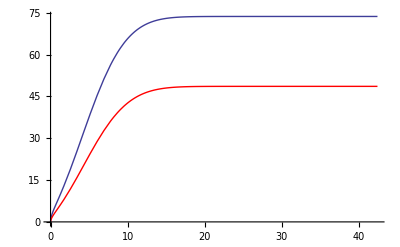

```mathematica
Show[
Plot[SAR[r],{r,0,10*Max[rvec]},PlotRange->{0,All}],
Plot[stSAR[r],{r,0,10*Max[rvec]},PlotRange->{0,All},PlotStyle->Red],
PlotRange->{0,All}
]
```

## Reef data

### Loading data and generating empirical PCF

Load data from reef fish

```mathematica
datadir="/Users/mmosmond/Documents/PHD/PCFinR/";
realdata=Import[datadir<>"sbc_fish_2010"<>".csv"];
```

The data comes with many columns

```mathematica
realdata[[1]]
```

{,Day,Month,Year,SampleDescription,Latitude,Longitude,Genus,Species,Abundance}

Lets first drop the row names, time, description, and genus

```mathematica
realdata=Drop[realdata,None,{1}];
realdata=Drop[realdata,None,{1}];
realdata=Drop[realdata,None,{1}];
realdata=Drop[realdata,None,{1}];
realdata=Drop[realdata,None,{1}];
realdata=Drop[realdata,None,{3}];
```

```mathematica
realdata[[1]]
```

{Latitude,Longitude,Species,Abundance}

Then drop the column names

```mathematica
realdata=Drop[realdata,1];
```

Get each variable of interest from data table

```mathematica
gx=Transpose[realdata][[1]];
gy=Transpose[realdata][[2]];
sp=Transpose[realdata][[3]];
ab=Transpose[realdata][[4]];
```

Define the spatial extent of the area of interest

```mathematica
Lx=Max[gx]-Min[gx];(*total x and y distance of area of interest, ie a grid with length Lx and width Ly*)
Ly=Max[gy]-Min[gy];
nbins=3;
Asub=Lx/nbins;(*space between coordinates, ie we chop up the total area into squares with length Asub; best if this divides the total space nicely, ie Lx/Asub and Ly/Asub are integers*)
```

We then translate the lat longs to start at (0,0)

```mathematica
gx=gx-Min[gx];
gy=gy-Min[gy];
```

Then the locations and bins look like

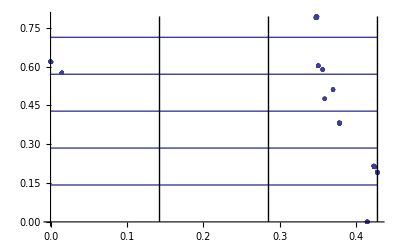

```mathematica
Show[
ListPlot[Transpose[{gx,gy}]],
Table[Plot[Asub*i,{x,0,Max[gx]}],{i,1,Ly/Asub}],
Epilog->{
Table[Line[{{Asub*i,0},{Asub*i,Max[gy]}}],{i,1,nbins}]
}
]
```

This is how many locations we have

```mathematica
Dimensions[Union[Transpose[{gx,gy}]]][[1]]
```

39

Some summary statistics of the data

```mathematica
Uspecie=Union[sp];(*vector of species IDs*)
Nspecies=Length[Uspecie];(*total number of species*)
TotAbundance=Total[ab];(*total abundance, across all species*)
```

Defining the coordinate system of the area

```mathematica
allpos=Tuples[{Range[Lx/Asub],Range[Ly/Asub]}]; (*coordinates, in translated form, ie. {1,1}, {1,2}, ..., {2,1}, {2,2}, ..., {m,n}*)
xyCpos=Flatten[Table[{(2 i+1)/2,(2 j+1)/2}// N,{i,0,(Lx/Asub)-1,1},{j,0,(Ly/Asub)-1,1}],1];(*halfway points between coordinates, which we use later to derive the distances between centers of each "bin" (area below (south) and to left (west) of each coordinate*)
allpair=Tuples[{allpos,allpos}];(*pairs of each translated coordinate with each other, e.g., {{1,1},{1,1}}*)
nplot=Range[Length[allpos]]; (*total number of coordinates/bins*)
```

Locations of plots (the bin they are in)

```mathematica
(*Xpos[p_]:=Flatten[Position[gx,x_?(Asub*(p-1) ≤ #<Asub*p&)],1]*)
Xpos[p_]:=Flatten[Position[gx,x_?(Asub*(p-1) <#≤ Asub*p&)],1]
(*which plots (their position in the data vector) have x location between two coordinates, for all pairs of x coordinates; for p between 1 and Lx/Asub*)
(*Ypos[q_]:=Flatten[Position[gy,x_?(Asub*(q-1) ≤ #<Asub*q&)],1]*)
Ypos[q_]:=Flatten[Position[gy,x_?(Asub*(q-1)<#≤Asub*q&)],1]
(*which plots have y location between two coordinates, for all pairs of y coordinates; for q between 1 and Ly/Asub*)
rule1=Flatten[Table[{allpos[[i]] -> nplot[[i]]},{i,1,Length[allpos]}],1];(*translate from coordinates (tuple) to single identifying number*)
rule2=Flatten[Table[{nplot[[i]] -> allpos[[i]]},{i,1,Length[allpos]}],1];(*translate back*)
XYpos[{p_,q_}]:=Intersection[Xpos[p],Ypos[q]];(*which plots have location (x,y) within (x(p-1),x p) and (y(p-1), y p)*)
possub=ParallelMap[XYpos,allpos];(*which plots fall in which bin (e.g., (x,y)=(321,434), with Asub=100, would fall in (400,500)*)
```

Which species are where

```mathematica
XYS[i_]:=Transpose[{gx[[possub[[i]]]],gy[[possub[[i]]]],sp[[possub[[i]]]]}];(*gives (x,y) location of plots, and sp code, in each bin*)
(*SabA[i_]:=Count[sp[[possub[[i]]]],#]&/@ Uspecie*) (*number of plots with each species in each bin*)
(*SabA[i_]:=(Count[sp[[possub[[i]]]],#]&/@ Uspecie)*ab[[possub[[i]]]]*)(*number of plots of each species in each bin*)
SabA[i_]:=Table[Sum[ab[[possub[[i]]]][[k]],{k,Flatten[(Position[sp[[possub[[i]]]],#]&/@ Uspecie)[[j]]]}],{j,1,Dimensions[Uspecie][[1]]}] (*number of plots * abundance in that plot of each species in each bin*)
(*SA[i_]:=Boole/@ (MemberQ[sp[[possub[[i]]]],#]&/@ Uspecie) *)(*1 if at least one plot with a species in given bin, ie presence/absence in bin*)
SA[i_]:=Boole[#>0]&/@SabA[i]
Spos=Table[SA[i],{i,1,Length[possub]}];(*table with all bins*)
```

Covariance in species abundance by distances

```mathematica
dist[{i_,j_}]:=Sqrt[Total[(Abs[xyCpos[[i]]-xyCpos[[j]]])^2]] (*Euclidean distance between center of two bins (in translated space; need to multiply by Asub to get real distances, which we do later)*)
index[{i_,j_}]:={i,j}(*not sure what this does, but doesnt hurt*)
alldist=Map[dist,allpair/.rule1]; (*distance between center of all pairs of bins*)
rvec=Union[alldist];(*all unique distances in increasing order*)
indexpair=Map[index,allpair/. rule1];(*translate from tuples of coordinates to pairs of coordinate indices*)
posdist=Position[alldist,#]&/@ rvec;(*identify coordinate index pairs whose bin centers are given distance apart*)
Cov[{i_,j_}]:=If[Total[SabA[i]]≠0&&Total[SabA[j]]≠0,Mean[SabA[i] SabA[j]]/(Mean[SabA[i]] Mean[SabA[j]])//N,Null];(*"covariance" in number of plots with species across bins, note that the "covariance" is taken over all species, ie "covariance" in community composition; only computes if some data in a bin - to prevent zero denominators*)
```

This function can take a while to run (if too long increase Asub)

```mathematica
allcov=Table[ParallelMap[Cov,indexpair[[Flatten[posdist[[i]],1]]]],{i,1,Length[rvec]}];(*covariance in number of plots with species at each distance*)
```

Remove Nulls (no data)

```mathematica
newallcov=Table[DeleteCases[allcov[[i]],Null],{i,1,Dimensions[allcov][[1]]}];
```

Our empirical correlation function

```mathematica
empPCF=Transpose[{rvec*Asub,Map[Mean,newallcov]}];(*empirical correlation function, PCF; first element of each pair is the (untranslated) distance between the center of two bins (rvec*Asub), the second element is the mean covariance in number of plots with species across all pairs of bins that distance apart*)
```

Delete Nulls

```mathematica
empPCF=Select[empPCF,NumberQ[#[[2]]]&];
```

which looks like this

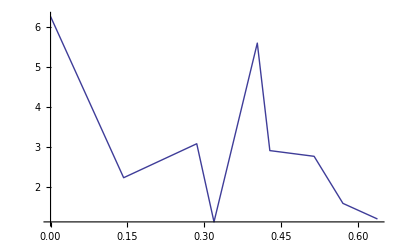

```mathematica
ListPlot[empPCF,Joined->True]
```

Method assumes number of individuals grows linearly with increasing size. Check:

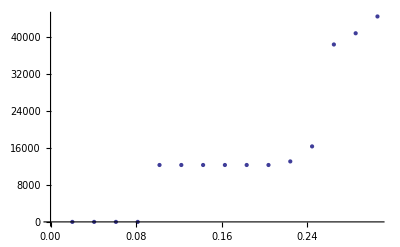

```mathematica
ListPlot[
Table[{j*Asub^2,Sum[Total[possub[[i]]],{i,1,j}]},{j,1,Max[nplot]}],
Joined->False
]
```

### Fitting the function to the data

```mathematica
g[r_]:=1/(2π)(ρ/λ)^2 BesselK[0,r/λ](*function to fit to the empirical PCF*)
λ=.;(*what does this do?*)
ρ=.;
fitcor=NonlinearModelFit[Rest[empPCF],g[r],{{λ,2},{ρ,50}},r];(*fit the function, with some parameter guesses*)
```

How good is the fit?

```mathematica
Grid[Transpose[{#,fitcor[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment -> Left](*stats for fit*)
```

AdjustedRSquared | 0.714361
AIC | 33.4466
BIC | 33.6849
RSquared | 0.78577

What are our parameter estimates?

```mathematica
fitcor["ParameterTable"](*stats for parameter estimates*)
σλ1=fitcor["ParameterTableEntries"][[1,2]];(*standard error for lambda*)
σρ1=fitcor["ParameterTableEntries"][[2,2]];(*standard error for rho*)(*standard error for rho*)
```

| Estimate | Standard Error | t-Statistic | P-Value
λ | 14886.7 | 809243. | 0.0183958 | 0.98592
ρ | 18305.1 | 948637. | 0.0192962 | 0.98523

Or if you like confidence intervals better...

```mathematica
fitcor["ParameterConfidenceIntervalTable"](*get confidence intervals too*)
```

| Estimate | Standard Error | Confidence Interval
λ | 14886.7 | 809243. | {-1.96526×10^6,1.99503×10^6}
ρ | 18305.1 | 948637. | {-2.30293×10^6,2.33954×10^6}

Plot fitted curve with data points

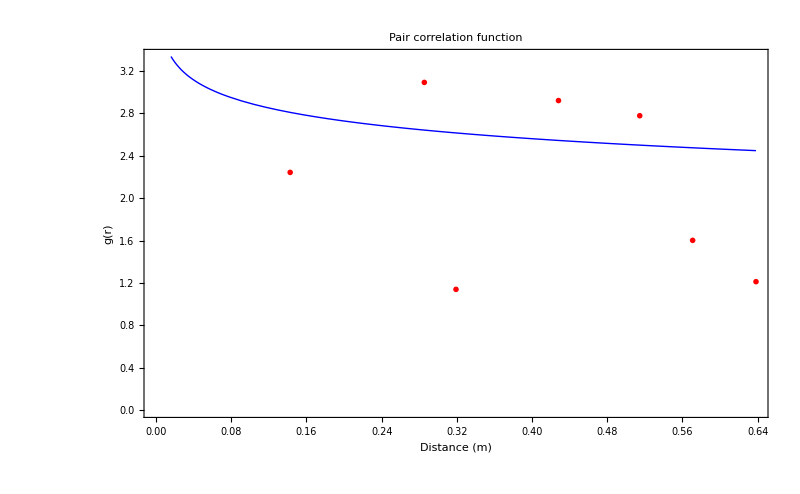

```mathematica
Plot[
fitcor[r],
{r,Min[rvec*Asub],Max[rvec*Asub]},
PlotStyle->{ Blue,Thick},
PlotRange->{{0,Max[rvec*Asub]},{0,Automatic}},
Frame ->{{True,False},{True,False}},
FrameLabel -> {"Distance (m)","g(r)"},
PlotLabel -> "Pair correlation function",
LabelStyle -> {FontFamily -> "Times",FontSize -> 12},
Prolog -> {Red,PointSize[0.005],Point/@ empPCF},
Axes->False,
ImageSize->800
]
```

Plot fitted curve with confidence bands

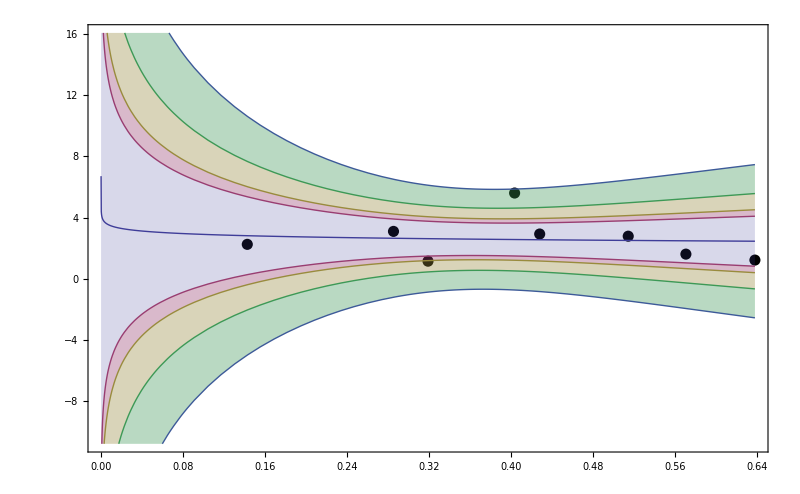

```mathematica
{bands90[x_],bands95[x_],bands99[x_],bands999[x_]} =Table[fitcor["MeanPredictionBands",ConfidenceLevel -> cl],{cl,{.9,.95,.99,.999}}];(*confidence bands*)
Show[
ListPlot[Rest[empPCF],PlotStyle->{Black,PointSize[0.01]},Axes->False],Plot[{fitcor[r],bands90[r],bands95[r],bands99[r],bands999[r]},{r,Min[rvec*Asub],Max[rvec*Asub]},Filling-> {2 ->{1},3 ->{2},4 ->{3},5 ->{4}}],
PlotRange->{{0,Max[rvec*Asub]},{0,Automatic}},
Frame->{True,True,False,False},
ImageSize->800]
```

### SAD and SAR plots

```mathematica
(* total number of individuals in each plot, across all spp *)
ind=Table[Total[SabA[i]],{i,1,Max[nplot]}];
```

```mathematica
(* shape parameters of the Gamma distribution, α and β, eqns 7 and 8 *)
α2p[L_]:=π (L/ρ)^2(1-(2λ)/L(BesselK[1,L/λ]BesselI[1,L/λ])/(BesselK[1,L/λ]BesselI[0,L/λ] + BesselK[0,L/λ]BesselI[1,L/λ]))^-1;
β2[L_]:=(Total[ind]/(Nspecies*Lx*Ly))*ρ^2(1-(2λ)/L(BesselK[1,L/λ]BesselI[1,L/λ])/(BesselK[1,L/λ]BesselI[0,L/λ] + BesselK[0,L/λ]BesselI[1,L/λ]));
```

```mathematica
(* q and the integral of q over distances L, eqn 10 and its integral over L *)
rsapres2medp[n_,L_]:=CDF[GammaDistribution[α2p[L],β2[L]],2^(n+1)]-CDF[GammaDistribution[α2p[L],β2[L]],2^n];
sarmedp[L_]:=1-CDF[GammaDistribution[α2p[L],β2[L]],1];
```

```mathematica
(*sSAD, eqn 9; downscaled in sense that only valid for r < max radius sampled*)
SAD[n_,r_]:=Nspecies*rsapres2medp[n,r]/sarmedp[ ((Lx*Ly)/π)^(1/2)]/.fitcor["BestFitParameters"];
```

```mathematica
(*beginning to think about preston classes*)
prest[1]=Mean[Table[Total[SA[i]],{i,1,Max[nplot]}]]//N (*mean number of species in one bin*)
prest[2]=Mean[Map[Mean,Table[Total[Boole[#>0]&/@(SA[i]+SA[j])-SA[i]],{i,1,Max[nplot]},{j,1,Max[nplot]}]]]//N (*mean number of species gained by sampling two bins instead of one*)
(*Mean[Map[Mean,Table[Total[Boole[#>0]&/@(SA[i]+SA[j]+SA[k])-Boole[#>0]&/@(SA[i]+SA[j])],{i,1,Max[nplot]},{j,1,Max[nplot]},{k,1,Max[nplot]}]]]//N *)(*mean number of species gained by sampling three bins instead of two*)
```

6.73333

4.98667

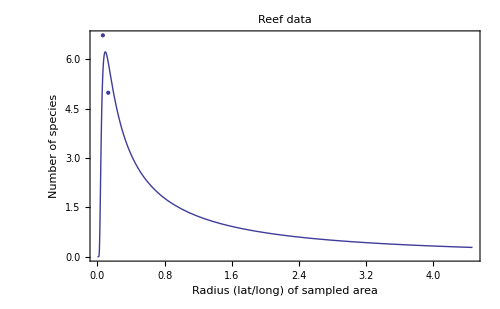

```mathematica
Show[
Plot[SAD[n,r]/.n->1,{r,0,Max[rvec]},PlotRange->{{0,Max[rvec]},{0,All}}],
ListPlot[Table[{π Asub^2*i,prest[i]},{i,1,2}]],
PlotRange->{{0,Max[rvec]},{0,All}},
Frame->{True,True,False,False},
PlotLabel->"Reef data",
FrameLabel->{"Radius (lat/long) of sampled area", "Number of species"},
ImageSize->500
]
```

```mathematica
(*SAR, eqn 11; downscaled in sense that only valid for r < max radius sampled*)
SAR[r_]:=Nspecies*sarmedp[r]/sarmedp[ ((Lx*Ly)/π)^(1/2)]/.fitcor["BestFitParameters"];
```

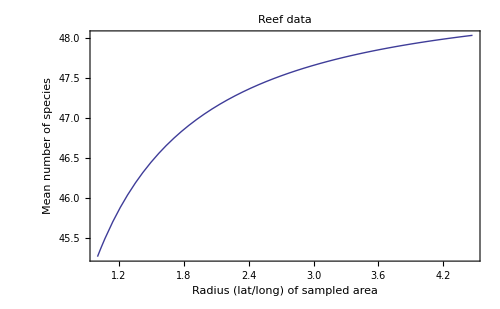

```mathematica
Plot[
SAR[r],{r,rvec[[2]],Max[rvec]},
PlotRange->{{0,Max[rvec]},{0,All}},
Frame->{True,True,False,False},
PlotLabel->"Reef data",
FrameLabel->{"Radius (lat/long) of sampled area", "Mean number of species"},
ImageSize->500
]
```

```mathematica
(* extrapolate to get number of spp if we sampled more area*)
upRichness=Nspecies*(sarmedp [((Lx*Ly)/π)^(1/2)])/(sarmedp [((samp*Asp)/π)^(1/2)]);(* Subscript[S, up](Subscript[R, 0]), p. 328; samp is number of samples, and Asp is area of each sample *)
dens=Total[ind]/Nspecies; (*avg density per species in sampled area*)
UPdens=Nspecies*dens/upRichness; (*mean density per species*)
```

```mathematica
(* disconnected SAR *)
downSAR[r_]:=upRichness*sarmedp[r]/sarmedp[((Lx*Ly)/π)^(1/2)];
```

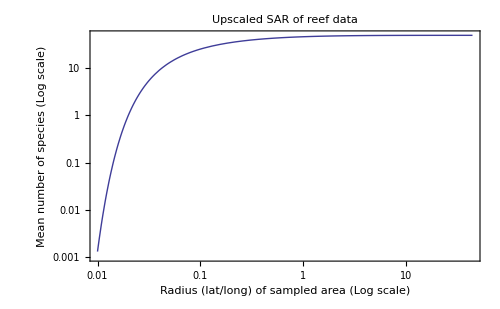

```mathematica
LogLogPlot[downSAR[r]/.fitcor["BestFitParameters"]/.Asp->Lx*Ly*0.012/.samp->60,{r,0.01,10*Max[rvec]},
PlotRange->{0.001,All},
Frame->{True,True,False,False},
PlotLabel->"Upscaled SAR of reef data",
FrameLabel->{"Radius (lat/long) of sampled area (Log scale)", "Mean number of species (Log scale)"},
ImageSize->500
]
```